```mathematica
Needs["ErrorBarPlots`"]
Get["/Users/kimdahee/mathematica/ErrorBarLogPlots/ErrorBarLogPlots.m"];
```

```mathematica
Xmin={1,1.16,1.33,1.51,1.71,1.92,2.15,2.40,2.67,2.97,3.29,3.64,4.02,4.43,4.88,5.37,5.90,6.47,7.09,7.76,8.48,9.26,10.1,11.0,12.0,13.0,14.1,15.3,16.6,18.0,19.5,21.1,22.8,24.7,26.7,28.8,31.1,33.5,36.1,38.9,41.9,45.1,48.5,52.2,56.1,60.3,64.8,69.7,74.9,80.5,93.0,108,125,147,175,211,259};
```

```mathematica
Length[Xmin ]
```

57

```mathematica
Xmax={1.16,1.33,1.51,1.71,1.92,2.15,2.40,2.67,2.97,3.29,3.64,4.02,4.43,4.88,5.37,5.90,6.47,7.09,7.76,8.48,9.26,10.1,11.0,12.0,13.0,14.1,15.3,16.6,18.0,19.5,21.1,22.8,24.7,26.7,28.8,31.1,33.5,36.1,38.9,41.9,45.1,
48.5,52.2,56.1,60.3,64.8,69.7,74.9,80.5,93.0,108,125,147,175,211,259,450};
```

```mathematica
Length[Xmax]
```

57

```mathematica
Y={5.94*10^-3,5.57*10^-3,9.75*10^-3,1.06*10^-2,1.25*10^-2,1.40*10^-2,1.50*10^-2,1.64*10^-2,1.64*10^-2,1.69*10^-2,1.67*10^-2,1.59*10^-2,1.56*10^-2,1.43*10^-2,1.23*10^-2,1.12*10^-2,9.80*10^-3,8.69*10^-3,7.59*10^-3,6.54*10^-3,5.46*10^-3,4.67*10^-3,3.96*10^-3,3.23*10^-3,2.65*10^-3,2.23*10^-3,1.85*10^-3,1.49*10^-3,1.19*10^-3,9.53*10^-4,7.72*10^-4,6.33*10^-4,5.02*10^-4,4.11*10^-4,3.32*10^-4,2.68*10^-4,2.07*10^-4,1.75*10^-4,1.40*10^-4,1.10*10^-4,8.78*10^-5,7.05*10^-5,5.89*10^-5,4.82*10^-5,3.99*10^-5,3.09*10^-5,2.43*10^-5,2.06*10^-5,1.78*10^-5,1.22*10^-5,7.86*10^-6,5.09*10^-6,3.39*10^-6,2.08*10^-6,1.33*10^-6,9.11*10^-7,2.13*10^-7};
```

```mathematica
Length[Xmin]
```

57

```mathematica
Subscript[m, p]=0.9383
```

0.9383

```mathematica
Xmed=0.5*(Xmin+Xmax);
```

```mathematica
(* KXmed=Flatten[Table[{(Subscript[m, p]^2+Xmed[[i]]^2)^(1/2)-Subscript[m, p]},{i,1,Length[Xmax]}],1] *)
KXmin=Flatten[Table[{(Subscript[m, p]^2+Xmin[[i]]^2)^(1/2)-Subscript[m, p]},{i,1,Length[Xmax]}],1];
KXmax=Flatten[Table[{(Subscript[m, p]^2+Xmax[[i]]^2)^(1/2)-Subscript[m, p]},{i,1,Length[Xmax]}],1];
KXmed=Flatten[Table[{(KXmin[[i]]+KXmax[[i]])/2},{i,1,Length[Xmax]}],1];
```

```mathematica
(* KX=Flatten[Table[{(KXmin[[i]]+KXmax[[i]])/2},{i,1,Length[KXmax]}],1]; *)

 KX=Flatten[Table[{(Subscript[m, p]^2+(Xmed[[i]])^2)^(1/2)-Subscript[m, p]},{i,1,Length[Xmax]}],1];
```

```mathematica
KErrTab=Table[{KX[[i]],((Subscript[m, p]^2+Xmed[[i]]^2)^(1/2))/Xmed[[i]]*Y[[i]]*KX[[i]]^2},{i,1,Length[Xmin]}];
```

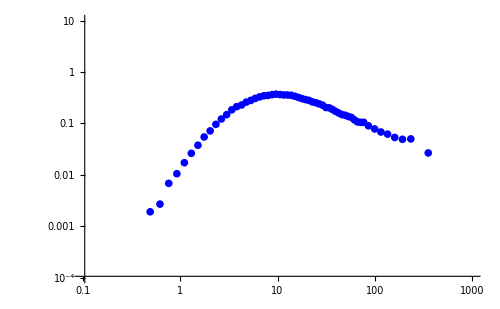

```mathematica
ErrPlo1=ListLogLogPlot[KErrTab,PlotRange->{{0.1,1000},{10^-4,10}},PlotStyle->Blue,ImageSize->500]
```

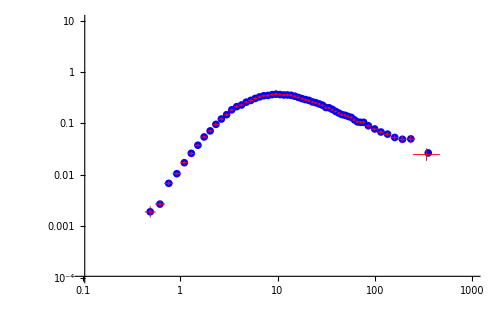

```mathematica
Show[ErrPlo1,ErroPlot]
```

```mathematica
Subscript[σ, stat]={1.31*10^-3,0.68*10^-3,0.68*10^-3,0.05*10^-2,0.05*10^-2,0.05*10^-2,0.05*10^-2,0.04*10^-2,0.04*10^-2,0.04*10^-2,0.03*10^-2,0.03*10^-2,0.04*10^-2,0.03*10^-2,0.02*10^-2,0.02*10^-2,0.13*10^-3,0.11*10^-3,0.09*10^-3,0.08*10^-3,0.06*10^-3,0.03*10^-3,0.03*10^-3,0.02*10^-3,0.02*10^-3,0.02*10^-3,0.02*10^-3,0.01*10^-3,0.01*10^-3,0.08*10^-4,0.07*10^-4,0.06*10^-4,0.05*10^-4,0.04*10^-4,0.04*10^-4,0.03*10^-4,0.03*10^-4,0.02*10^-4,0.02*10^-4,0.02*10^-4,0.20*10^-5,0.18*10^-5,0.16*10^-5,0.14*10^-5,0.13*10^-5,0.11*10^-5,0.09*10^-5,0.08*10^-5,0.08*10^-5,0.04*10^-5,0.35*10^-6,0.29*10^-6,0.24*10^-6,0.20*10^-6,0.19*10^-6,1.42*10^-7,0.51*10^-7};
```

```mathematica
Length[Subscript[σ, stat]]
```

57

```mathematica
Subscript[σ, sys]={0.58*10^-3,0.51*10^-3,0.68*10^-3,0.07*10^-2,0.08*10^-2,0.08*10^-2,0.09*10^-2,0.09*10^-2,0.09*10^-2,0.09*10^-2,0.09*10^-2,0.08*10^-2,0.08*10^-2,0.07*10^-2,0.06*10^-2,0.05*10^-2,0.45*10^-3,0.39*10^-3,0.34*10^-3,0.29*10^-3,0.24*10^-3,0.20*10^-3,0.17*10^-3,0.14*10^-3,0.11*10^-3,0.09*10^-3,0.08*10^-3,0.06*10^-3,0.05*10^-3,0.37*10^-4,0.29*10^-4,0.23*10^-4,0.18*10^-4,0.14*10^-4,0.11*10^-4,0.08*10^-4,0.06*10^-4,0.05*10^-4,0.04*10^-4,0.03*10^-4,0.26*10^-5,0.21*10^-5,0.17*10^-5,0.14*10^-5,0.12*10^-5,0.10*10^-5,0.08*10^-5,0.07*10^-5,0.07*10^-5,0.05*10^-5,0.34*10^-6,0.24*10^-6,0.17*10^-6,0.12*10^-6,0.11*10^-6,0.93*10^-7,0.29*10^-7};
```

```mathematica
Length[Subscript[σ, sys]]
```

57

```mathematica
σ=(Subscript[σ, stat]^2+Subscript[σ, sys]^2)^(1/2);
```

```mathematica
FErrT=Table[{KX[[i]],((Subscript[m, p]^2+Xmed[[i]]^2)^(1/2))/Xmed[[i]]*Y[[i]]*KX[[i]]^2,KXmin[[i]],KXmax[[i]],((Subscript[m, p]^2+Xmed[[i]]^2)^(1/2))/Xmed[[i]]*(Y[[i]]-σ[[i]])*KX[[i]]^2,((Subscript[m, p]^2+Xmed[[i]]^2)^(1/2))/Xmed[[i]]*(Y[[i]]+σ[[i]])*KX[[i]]^2},{i,1,Length[KXmax]}];
```

```mathematica
FErrT1=Table[{FErrT[[i,1]],FErrT[[i,2]],(FErrT[[i,4]]-FErrT[[i,3]])/2,(FErrT[[i,6]]-FErrT[[i,5]])/2},{i,1,Length[KXmax]}];
```

```mathematica
ErroSet1=FErrT1/.{x_,y_,z_,k_}->{{x,y},ErrorBar[z,k]};
```

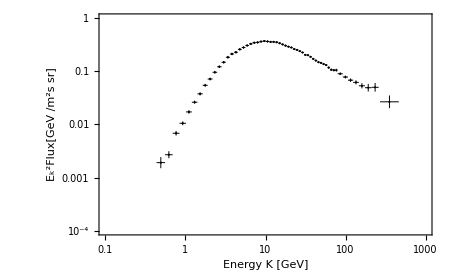

```mathematica
ErroPlot11=ErrorListLogLogPlot[ErroSet1,Frame->True,Axes->False,PlotRange->{{10^-1,10^3},{10^-4,1}}, ErrorBarFunction->Automatic,ImageSize->450,PlotStyle->{Black,AbsolutePointSize[1.5],AbsoluteThickness[0.7]},FrameLabel->{"Energy K [GeV]","E_k^2Flux[GeV /m^2s sr]"}]
```

```mathematica
(*Export["Error_data_AMS02.dat",FErrT1,"Table"]*)
Export["Error_data_AMS02_Full.dat",FErrT,"Table"]
```

Error_data_AMS02_Full.dat

```mathematica
IError=Import["/Users/kimdahee/Desktop/Master/paper_data/Error_data_AMS02.dat","Table",HeaderLines->1];
```

```mathematica
IError1=IError/.{x_,y_,z_,k_}->{{x,y},ErrorBar[z,k]};
```

```mathematica
ErroPlot11=ErrorListLogLogPlot[IError1,Frame->True,Axes->False,PlotRange->{{10^-1,10^3},{10^-4,1}}, ErrorBarFunction->Automatic,ImageSize->450,PlotStyle->{Black,AbsolutePointSize[1.5],AbsoluteThickness[0.7]},FrameLabel->{"Energy K [GeV]","E_k^2Flux[GeV /m^2s sr]"}]
```

-Graphics-